```mathematica
f[A_]:=Module[{},
solns={};
dim=Dimensions[A];
stack={{A,{}}};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
board=First[cur];
zeroes=Position[board,0,{2}];
If[zeroes=={},AppendTo[solns,cur],
pos=First[zeroes];
If[dim[[2]]≥ pos[[2]]+2,
If[board[[Apply[Sequence,pos+{0,1}]]]==0&&board[[Apply[Sequence,pos+{0,2}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{0,1},pos+{0,2}}->1],Append[cur[[2]],{pos,{0,1},3}]}]]];
If[dim[[2]]≥ pos[[2]]+3,
If[board[[Apply[Sequence,pos+{0,1}]]]==0&&board[[Apply[Sequence,pos+{0,2}]]]==0&&board[[Apply[Sequence,pos+{0,3}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{0,1},pos+{0,2},pos+{0,3}}->2],Append[cur[[2]],{pos,{0,1},4}]}]]];
If[dim[[2]]≥ pos[[2]]+2&&dim[[1]]≥ pos[[1]]+2,
If[board[[Apply[Sequence,pos+{1,1}]]]==0&&board[[Apply[Sequence,pos+{2,2}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,1},pos+{2,2}}->3],Append[cur[[2]],{pos,{1,1},3}]}]]];
If[dim[[2]]≥ pos[[2]]+3&&dim[[1]]≥ pos[[1]]+3,
If[board[[Apply[Sequence,pos+{1,1}]]]==0&&board[[Apply[Sequence,pos+{2,2}]]]==0&&board[[Apply[Sequence,pos+{3,3}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,1},pos+{2,2},pos+{3,3}}->4],Append[cur[[2]],{pos,{1,1},4}]}]]];If[dim[[1]]≥ pos[[1]]+2,
If[board[[Apply[Sequence,pos+{1,0}]]]==0&&board[[Apply[Sequence,pos+{2,0}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,0},pos+{2,0}}->5],Append[cur[[2]],{pos,{1,0},3}]}]]];
If[dim[[1]]≥ pos[[1]]+3,
If[board[[Apply[Sequence,pos+{1,0}]]]==0&&board[[Apply[Sequence,pos+{2,0}]]]==0&&board[[Apply[Sequence,pos+{3,0}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,0},pos+{2,0},pos+{3,0}}->6],Append[cur[[2]],{pos,{1,0},4}]}]]];
If[pos[[2]]>2&&dim[[1]]≥ pos[[1]]+2,
If[board[[Apply[Sequence,pos+{1,-1}]]]==0&&board[[Apply[Sequence,pos+{2,-2}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,-1},pos+{2,-2}}->3],Append[cur[[2]],{pos,{1,-1},3}]}]]];
If[pos[[2]]>3&&dim[[1]]≥ pos[[1]]+3,
If[board[[Apply[Sequence,pos+{1,-1}]]]==0&&board[[Apply[Sequence,pos+{2,-2}]]]==0&&board[[Apply[Sequence,pos+{3,-3}]]]==0,PrependTo[stack,{ReplacePart[board,{pos,pos+{1,-1},pos+{2,-2},pos+{3,-3}}->4],Append[cur[[2]],{pos,{1,-1},4}]}]]];
]]]
```

```mathematica
redline[{t1_,t2_,t3_}]:=Line[{t1+{1/2,1/2},t1+(t3-1)t2+{1/2,1/2}}]
```

```mathematica
s[{x_,y_}]:=Line[{{x,y},{x+1,y},{x+1,y+1},{x,y+1},{x,y}}]
```

```mathematica
boxes[L_]:=Map[s,Select[Position[L,x_/;(1≤x≤8),{2}],Not[MemberQ[#,0]]&]]
```

```mathematica
pic[L_]:=Module[{},
dim=Dimensions[L[[1]]];
Style[Graphics[{boxes[L[[1]]],Red,AbsoluteThickness[4],Map[redline[#]&,L[[2]]]
},ImageSize->15dim],Antialiasing->False]]
```

```mathematica
blankpic[L_,letters_]:=Module[{},
dim=Dimensions[L[[1]]];
Style[Graphics[{boxes[L[[1]]],Map[Text[Style[name[#[[3]]],FontSize->10],{#[[1]]+1/2,#[[2]]+1/2}]&,letters]
},ImageSize->15dim],Antialiasing->False]]
```

```mathematica
missingpic[L_,letters_,missing_]:=Module[{},
dim=Dimensions[L[[1]]];
Style[Graphics[{boxes[L[[1]]],Rectangle[missing,missing+{1,1}],Map[Text[name[#[[3]]],{#[[1]]+1/2,#[[2]]+1/2}]&,letters]
},ImageSize->15dim],Antialiasing->False]]
```

```mathematica
pic[{Table[1,{7},{5}],{}}]
```

-Graphics-

```mathematica
type[1]={3,4};
name[1]="D";
type[2]={1,2};
name[2]="V";
type[3]={5,6};
name[3]="H";
type[4]={1,3,5};
name[4]="3";
type[5]={2,4,6};
name[5]="4";
```

4, 4, 14
4, 5, 26
4, 6, 57
4, 7, 177
4, 8, 459
4, 9, 1048
4, 10, 2715
5, 5, 16
5, 6, 123
5, 7, 788
5, 8, 1883
5, 9, 4686
5, 10, 24818
6, 6, 412
6, 7, 3491
6, 8, 13453
6, 9, 44569
7, 7, 24812
7, 8, 155551

```mathematica
height=4;
width=10;
For[ii=1,ii≤Floor[(width+1)/2],ii++,
For[jj=1,jj≤Floor[(height+1)/2],jj++,
For[iii=ii,iii≤width+1-ii,iii++,
For[jjj=1,jjj≤height,jjj++,
f[ReplacePart[Table[0,{width},{height}],{{ii,jj},{iii,jjj}}->-1]];
If[Length[solns]==1,Print[blankpic[solns[[1]],{}]];Print[pic[solns[[1]]]]];
]]]]
```

```mathematica
height=5;
width=9;
For[ii=1,ii≤Floor[(width+1)/2],ii++,
For[jj=1,jj≤Floor[(height+1)/2],jj++,
For[iii=ii,iii≤width+1-ii,iii++,
For[jjj=1,jjj≤height,jjj++,
f[ReplacePart[Table[0,{width},{height}],{{ii,jj},{iii,jjj}}->-1]];
If[Length[solns]==1,Print[blankpic[solns[[1]],{}]];Print[pic[solns[[1]]]]];
]]]]
```

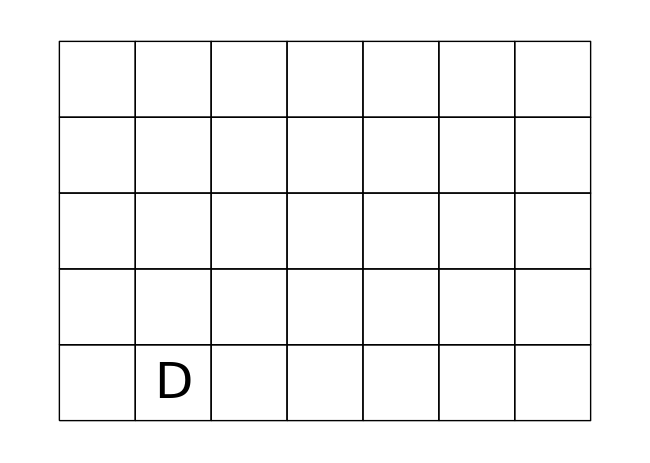

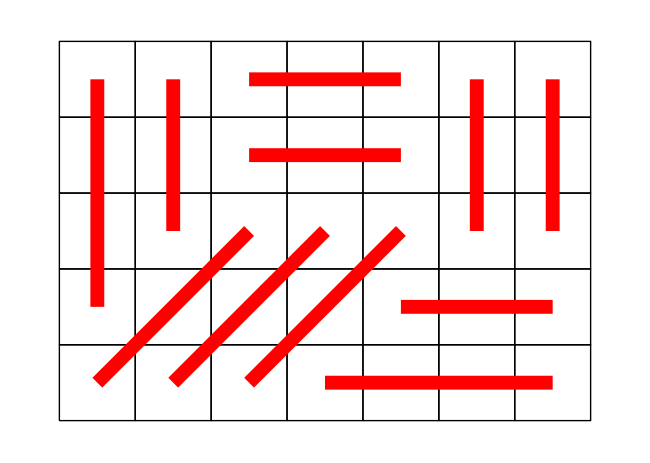

```mathematica
height=5;
width=7;
f[Table[0,{width},{height}]];
For[i1=1,i1≤Floor[(width+1)/2],i1++,
For[j1=1,j1≤Floor[(height+1)/2],j1++,
For[t1=1,t1≤5,t1++,
both=Select[solns,MemberQ[type[t1],#[[1,i1,j1]]]&];
If[Length[both]==1,Print[blankpic[both[[1]],{{i1,j1,t1}}]];Print[pic[both[[1]]]]];
]]]
```

```mathematica
height=6;
width=7;
f[Table[0,{width},{height}]];
For[i1=1,i1≤Floor[(width+1)/2],i1++,
For[j1=1,j1≤Floor[(height+1)/2],j1++,
For[t1=4,t1≤5,t1++,
For[i2=i1,i2≤width+1-i1,i2++,
For[j2=1,j2≤height,j2++,
For[t2=4,t2≤5,t2++,
For[i3=i2,i3≤width+1-i2,i3++,
For[j3=1,j3≤height,j3++,
For[t3=4,t3≤5,t3++,
both=Select[solns,MemberQ[type[t1],#[[1,i1,j1]]]&&MemberQ[type[t2],#[[1,i2,j2]]]&&MemberQ[type[t3],#[[1,i3,j3]]]&];
If[Length[both]==1,Print[blankpic[both[[1]],{{i1,j1,t1},{i2,j2,t2},{i3,j3,t3}}]];Print[pic[both[[1]]]]];
]]]]]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
height=5;
width=9;
f[Table[0,{width},{height}]];
For[i1=1,i1≤Floor[(width+1)/2],i1++,
For[j1=1,j1≤Floor[(height+1)/2],j1++,
For[t1=4,t1≤5,t1++,
For[i2=i1,i2≤width+1-i1,i2++,
For[j2=1,j2≤height,j2++,
For[t2=4,t2≤5,t2++,
For[i3=i2,i3≤width+1-i2,i3++,
For[j3=1,j3≤height,j3++,
For[t3=4,t3≤5,t3++,
both=Select[solns,MemberQ[type[t1],#[[1,i1,j1]]]&&MemberQ[type[t2],#[[1,i2,j2]]]&&MemberQ[type[t3],#[[1,i3,j3]]]&];
If[Length[both]==1,Print[blankpic[both[[1]],{{i1,j1,t1},{i2,j2,t2},{i3,j3,t3}}]];Print[pic[both[[1]]]]];
]]]]]]]]]
```

-Graphics-

-Graphics-

```mathematica
height=6;
width=8;
f[Table[0,{width},{height}]];
For[i1=1,i1≤Floor[(width+1)/2],i1++,
For[j1=1,j1≤Floor[(height+1)/2],j1++,
For[t1=4,t1≤5,t1++,
For[i2=i1,i2≤width+1-i1,i2++,
For[j2=1,j2≤height,j2++,
For[t2=4,t2≤5,t2++,
For[i3=i2,i3≤width+1-i2,i3++,
For[j3=1,j3≤height,j3++,
For[t3=4,t3≤5,t3++,
both=Select[solns,MemberQ[type[t1],#[[1,i1,j1]]]&&MemberQ[type[t2],#[[1,i2,j2]]]&&MemberQ[type[t3],#[[1,i3,j3]]]&];
If[Length[both]==1,Print[blankpic[both[[1]],{{i1,j1,t1},{i2,j2,t2},{i3,j3,t3}}]];Print[pic[both[[1]]]]];
]]]]]]]]]
```

```mathematica
height=7;
width=7;
f[Table[0,{width},{height}]];
For[i1=1,i1≤Floor[(width+1)/2],i1++,
For[j1=1,j1≤Floor[(height+1)/2],j1++,
For[t1=4,t1≤5,t1++,
For[i2=i1,i2≤width+1-i1,i2++,
For[j2=1,j2≤height,j2++,
For[t2=4,t2≤5,t2++,
For[i3=i2,i3≤width+1-i2,i3++,
For[j3=1,j3≤height,j3++,
For[t3=4,t3≤5,t3++,
both=Select[solns,MemberQ[type[t1],#[[1,i1,j1]]]&&MemberQ[type[t2],#[[1,i2,j2]]]&&MemberQ[type[t3],#[[1,i3,j3]]]&];
If[Length[both]==1,Print[blankpic[both[[1]],{{i1,j1,t1},{i2,j2,t2},{i3,j3,t3}}]];Print[pic[both[[1]]]]];
]]]]]]]]]
```

## 7x6

-Graphics-

-Graphics-

-Graphics-

«421 more identical outputs»

## 9x5

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## 8x6

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

$Aborted

## 7x7

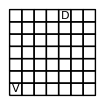

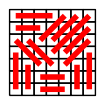

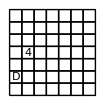

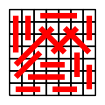

## 10x5

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## 9x6

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## 8x7

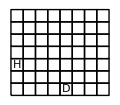

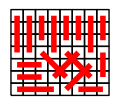

## 10x4 hole

-Graphics-

-Graphics-

## 7x6 hole

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## 9x5 hole

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## 8x6 hole

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## 7x7 hole

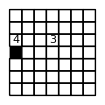

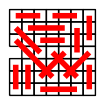

## 7x5 - 2 holes *

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## 7x5 - 3 numbers *

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»